## ANALYSIS OF SINGLE CELL VIRUS INFECTIONS

### Introduction

Please

run: Evaluation -> Evaluate Initialization Cells

Make sure: "Evaluation -> Dynamic Updating Enabled" is selected

before using this notebook

```mathematica
Clear["Global`*"]
```

The main idea is to model behaviour of infections in a single cell with a functional model.

The data can be classified into 3 main groups by just bare eye investigation

The ones with no infection

the ones with infection, but stay alive at the end of the experiment

Ones that die because of infection before experiment ends

One candinate model might be

A single line to represent data with no infection

A sigmoidal function to represent cases, with infection but cell stays alive at the end of experiment

A double sigmoidal function or a variant of it that can explain both start progress and end of the infection (i.e death of the cell)

Te aim of this text is to investigate possible candidates for a double sigmodal function

### Sigmoidal Function

A good start point for this is to investigate sigmoidal function that we are currently using for cases where cell keeps on living with infection

y=A+(Ka-A)/(1+ⅇ^(-B*(x-M)))

In this model variables have clear meaning related with behavior of the data

A represents the initial value of the sigmoidal curve

Ka represents the maximum height of the sigmoidal function

B is related the maximum slope of the sigmoidal function (B>0)

M represents the location on the x axis where the slope is maximum

Here is a simple sigmoidal function with changable variables

```mathematica
fSigmoidal[A_,Ka_,B_,M_,x_]=A+(Ka-A)/(1+ⅇ^(-B*(x-M)));
Manipulate[
Plot[fSigmoidal[A,Ka,B,M,x],{x,0,15},PlotRange->{0,1}],
{{A,0},0,1,.01},
{{Ka,1},0,1,.01},
{{B,1},0,10,.01},
{{M,8},0,15,.01}]
```

Lets look at the functions behaviour more deeply.

left and right limits should be equal to A and Ka respectively

Maximum of the slope should be occoured at point M (i.e. second derivarive of the function should be equal to 0 at x=M)

Slope of the function should be related with B at x is equal to M

```mathematica
Limit[fSigmoidal[A,Ka,B,M,x],x->-∞,Assumptions->{B>0}]
Limit[fSigmoidal[A,Ka,B,M,x],x->∞,Assumptions->{B>0}]
Solve[D[fSigmoidal[A,Ka,B,M,x],{x,2}]==0,x]
D[fSigmoidal[A,Ka,B,M,x],x]/.x->M (* As can be seen from the result the slope is also 
related with (Ka-A); i.e the width of the function. But if the data is normalized in 
such a way Ka=1 and A=0 slope is directly proportional to B*)
```

A

Ka

{{x→ConditionalExpression[(B M-2 ⅈ π C[1])/B,C[1]∈Integers]}}

1/4 B (-A+Ka)

If we change the sign in front of the slope term in sigmoidal function we get a decreasing sigmoidal function that starts from Ka parameter and ends in A parameter

y=A+(Ka-A)/(1+ⅇ^(B*(x-M)))

Lets see how this function behaves dynamically

```mathematica
fNegativeSigmoidal[A_,Ka_,B_,M_,x_]=A+(Ka-A)/(1+ⅇ^(B*(x-M)));
Manipulate[
Plot[fNegativeSigmoidal[A,Ka,B,M,x],{x,0,15},PlotRange->{0,1}],
{{A,0},0,1,.01},
{{Ka,1},0,1,.01},
{{B,1},0,10,.01},
{{M,8},0,15,.01}]
```

### Double Sigmoidal Function

#### First Try (multiplication sigmoidal)

The first try to find a model that can capture death is to use a function composed of multiplication of an increasing and a decreasing sigmodal functions

y=(A1+(Ka-A1)/(1+ⅇ^(-B1*(x-M1))))(A2+(1-A2)/(1+ⅇ^(B2*(x-(M1+L)))))

So the first term is related with increasing sigmoidal function and second term is related with decreasing sigmoidal function (B1>0 and B2>0).

The terms in the function are

A1 is the starting height of the function

A2 is the end height of the function

B1 is the slope for the increasing part of the function

B2 is the slope for decreasing part of the function

M1 is the point with highest slope (absolute value) for increasing part of the function

M1+L is the point with highest slope (absolute value) for decreasing part of the function (With a positive L one can speculate we are giving a boundry condition to the system saying death of the virus happens after infection)

Here is a simple double-multiplication sigmoidal function with changable variables

```mathematica
fMultiplicationSigmoidal[A1_,A2_,Ka_,B1_,M1_,B2_,L_,x_]=
											(A1+(Ka-A1)/(1+ⅇ^(-B1*(x-M1))))*(A2+(1-A2)/(1+ⅇ^(B2*(x-(M1+L)))));
Manipulate[
Plot[fMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,0,30},PlotRange->{0,1.2}],
{{A1,0},0,1,.01},
{{A2,0.2},0,1,.01},
{{Ka,1},0,1,.01},
{{B1,1},0,10,.01},
{{M1,8},0,20,.01},
{{B2,2},0,10,0.01},
{{L,10},0,10,0.001}]
```

The function satisfies some limit properties at ±∞

```mathematica
Limit[fMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],x->-∞,Assumptions->{B1>0,B2>0,L>0}]
Limit[fMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],x->∞,Assumptions->{B1>0,B2>0,L>0}]
```

A1

A2 Ka

Unfortunately first or second derivative of multiplication sigmoidal is so complicated it can not be solved algebrically to find

Positions where the slope is maximum

Value of the slope at this point

Location of the maximum (local & global) of the function

The maximum (local & global) of the function

```mathematica
Solve[D[fMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,1}]==0,x]
Reduce[{D[fMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,1}]==0, 
										B1>0,B2>0,L>0,Ka>A1,Ka>A2}, x, Reals]

Solve[D[fMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,2}]==0,x]
Reduce[{D[fMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,2}]==0, 
										B1>0,B2>0,L>0,Ka>A1,Ka>A2}, x, Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(B1 ⅇ^(-B1 (-M1+x)) (A2+(1-A2)/(1+ⅇ^(B2 (-L-M1+x)))) (-A1+Ka))/((1+ⅇ^(-B1 (-M1+x)))^2)-((1-A2) B2 ⅇ^(B2 (-L-M1+x)) (A1+(-A1+Ka)/(1+ⅇ^(-B1 (-M1+x)))))/((1+ⅇ^(B2 (-L-M1+x)))^2)==0,x]

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{(B1 ⅇ^(-B1 (-M1+x)) (A2+(1-A2)/(1+ⅇ^(B2 (-L-M1+x)))) (-A1+Ka))/((1+ⅇ^(-B1 (-M1+x)))^2)-((1-A2) B2 ⅇ^(B2 (-L-M1+x)) (A1+(-A1+Ka)/(1+ⅇ^(-B1 (-M1+x)))))/((1+ⅇ^(B2 (-L-M1+x)))^2)==0,B1>0,B2>0,L>0,Ka>A1,Ka>A2},x,Reals]

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(2 (1-A2) B1 B2 ⅇ^(-B1 (-M1+x)+B2 (-L-M1+x)) (-A1+Ka))/((1+ⅇ^(-B1 (-M1+x)))^2 (1+ⅇ^(B2 (-L-M1+x)))^2)+((2 B1^2 ⅇ^(-2 B1 (-M1+x)))/((1+ⅇ^(-B1 (-M1+x)))^3)-(B1^2 ⅇ^(-B1 (-M1+x)))/((1+ⅇ^(-B1 (-M1+x)))^2)) (A2+(1-A2)/(1+ⅇ^(B2 (-L-M1+x)))) (-A1+Ka)+(1-A2) ((2 B2^2 ⅇ^(2 B2 (-L-M1+x)))/((1+ⅇ^(B2 (-L-M1+x)))^3)-(B2^2 ⅇ^(B2 (-L-M1+x)))/((1+ⅇ^(B2 (-L-M1+x)))^2)) (A1+(-A1+Ka)/(1+ⅇ^(-B1 (-M1+x))))==0,x]

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{-(2 (1-A2) B1 B2 ⅇ^(-B1 (-M1+x)+B2 (-L-M1+x)) (-A1+Ka))/((1+ⅇ^(-B1 (-M1+x)))^2 (1+ⅇ^(B2 (-L-M1+x)))^2)+((2 B1^2 ⅇ^(-2 B1 (-M1+x)))/((1+ⅇ^(-B1 (-M1+x)))^3)-(B1^2 ⅇ^(-B1 (-M1+x)))/((1+ⅇ^(-B1 (-M1+x)))^2)) (A2+(1-A2)/(1+ⅇ^(B2 (-L-M1+x)))) (-A1+Ka)+(1-A2) ((2 B2^2 ⅇ^(2 B2 (-L-M1+x)))/((1+ⅇ^(B2 (-L-M1+x)))^3)-(B2^2 ⅇ^(B2 (-L-M1+x)))/((1+ⅇ^(B2 (-L-M1+x)))^2)) (A1+(-A1+Ka)/(1+ⅇ^(-B1 (-M1+x))))==0,B1>0,B2>0,L>0,Ka>A1,Ka>A2},x,Reals]

So one needs to go with numerical solutions...

The real problem with this model is that; "with some parameter sets the function behaves wierdly". Here is an example:

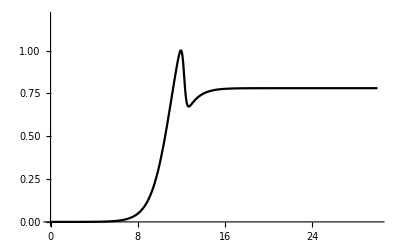

```mathematica
Plot[fMultiplicationSigmoidal[0,0.5368628,1.454867,1.084971,11.11337,8.529749,1.13329,x]
,{x,0,30},PlotRange->{0,1.2}]
```

It is kind of obvious to see the problem with bare eye, but it is hard to quantify the problem basically because the equations related with the derivatives (first & second order) of multiplication sigmoidal function are not solvable analytically. But after some investigation one can see that the problem is related the function reaches its right side limit from below, but we want it to reach its rightside limit from above. This is equivalent that; on the right limit the first derivative of the function approaches zero from above (the function is increasing), but we prefer the first derivative of the function reach zero in the right limit from below. The function should decrease!.

This can be seen more clearly if we look at the plot of the derivative of the same function.

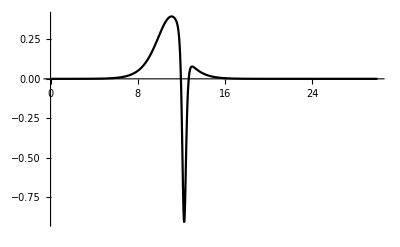

```mathematica
fDMultiplicationSigmoidal[A1_,A2_,Ka_,B1_,M1_,B2_,L_,x_]=
	D[fMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,1}];

Plot[fDMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,x]/.
	{A1->0,A2->0.5368628,Ka->1.454867,B1->1.084971,M1->11.11337,B2->8.529749,L->1.13329},
																{x,0,30},PlotRange->Full]
```

One way to quantify the problem is to look at the sign of derivative at a left far point & a right far point; say x=2000 and x=-2000 respectively. If it is -1 we are in a good shape if it is +1 we have a problem

```mathematica
xValue=2000;

Manipulate[

	Grid[
		{
		{StringForm["Sign of derivative is `` at Lim_(x → -∞); it should be +1",
							Sign[fDMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,-xValue]]]},
		{StringForm["Sign of derivative is `` at Lim_(x → ∞); it should be -1",
							Sign[fDMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,xValue]]]},
		{Plot[fMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,0,30},
							PlotRange->{-0.2,2},PlotLabel->Function,ImageSize->350]},
		{Plot[fDMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,0,30},
							PlotRange->Full,PlotLabel->Derivative,ImageSize->350]}
		}
	,Frame->All],

	{{A1,0},0,1,.01},
	{{A2,0.5368628},0,1,.01},
	{{Ka,1.454867},0,2,.01},
	{{B1,1.084971},0.01,10,.01},
	{{M1,11.11337},7.5-20,7.5+20,.01},
	{{B2,8.529749},0.01,10,0.01},
	{{L,1.13329},0,10,0.001}
]
```

After playing with variables for some time one will recognize that this value is +1 almost half of the time. Even with good looking graphs the value might be +1. Here is an example

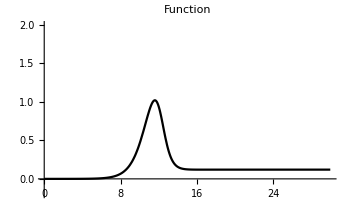
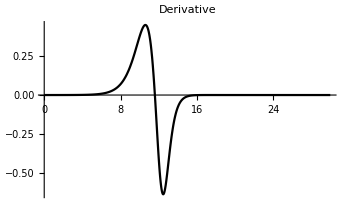
Sign of derivative is 1 at Lim_(x → -∞); it should be +1
Sign of derivative is 1 at Lim_(x → ∞); it should be -1
-Graphics-
-Graphics-

```mathematica
xValue=2000;
Subscript[A1, 0]=0; Subscript[A2, 0]=0.06; Subscript[Ka, 0]=2; Subscript[B1, 0]=1.08497; Subscript[M1, 0]=11.1134; Subscript[B2, 0]=2.14; Subscript[L, 0]=1.13329;

	Grid[
		{
		{StringForm["Sign of derivative is `` at Lim_(x → -∞); it should be +1",
			Sign[fDMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,-xValue]/.
				{A1->Subscript[A1, 0], A2->Subscript[A2, 0], Ka->Subscript[Ka, 0], B1->Subscript[B1, 0], M1->Subscript[M1, 0], B2->Subscript[B2, 0],L->Subscript[L, 0]}]]},
		{StringForm["Sign of derivative is `` at Lim_(x → ∞); it should be -1",
			Sign[fDMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,xValue]/.
				{A1->Subscript[A1, 0], A2->Subscript[A2, 0], Ka->Subscript[Ka, 0], B1->Subscript[B1, 0], M1->Subscript[M1, 0], B2->Subscript[B2, 0],L->Subscript[L, 0]}]]},
		{Plot[fMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,x]/.
				{A1->Subscript[A1, 0], A2->Subscript[A2, 0], Ka->Subscript[Ka, 0], B1->Subscript[B1, 0], M1->Subscript[M1, 0], B2->Subscript[B2, 0],L->Subscript[L, 0]},{x,0,30},
					PlotRange->{-0.2,2},PlotLabel->Function,ImageSize->350]},
		{Plot[fDMultiplicationSigmoidal[A1,A2,Ka,B1,M1,B2,L,x]/.
				{A1->Subscript[A1, 0], A2->Subscript[A2, 0], Ka->Subscript[Ka, 0], B1->Subscript[B1, 0], M1->Subscript[M1, 0], B2->Subscript[B2, 0],L->Subscript[L, 0]},{x,0,30},
					PlotRange->Full,PlotLabel->Derivative,ImageSize->350]}
		}
	,Frame->All]
```

It seems like if B2>B1 then we have a problem

#### Better Candidate (additive sigmoidal)

For generating a better candidate one can firstly start to simplify multiplication sigmoidal function (Item1Numbered). If we set A1 and A2 into 0 we will end up with

Ka/((1+ⅇ^(-B1*(x-M1)))*(1+ⅇ^(B2*(x-(M1+L)))))

This function also have two different slopes B1 and B2 for increasing and decreasing part, and it behaves as it should in the limit cases

```mathematica
xValue=2000;

fProtoAdditiveSigmoidal[Ka_,B1_,M1_,B2_,L_,x_]=Ka/((1+ⅇ^(-B1*(x-M1)))*(1+ⅇ^(B2*(x-(M1+L)))));
fDProtoAdditiveSigmoidal[Ka_,B1_,M1_,B2_,L_,x_]=
									D[fProtoAdditiveSigmoidal[Ka,B1,M1,B2,L,x],{x,1}];

Manipulate[

	Grid[
		{
		{StringForm["Sign of derivative is `` at Lim_(x → -∞); it should be +1",
								Sign[fDProtoAdditiveSigmoidal[Ka,B1,M1,B2,L,-xValue]]]},
		{StringForm["Sign of derivative is `` at Lim_(x → ∞); it should be -1",
								Sign[fDProtoAdditiveSigmoidal[Ka,B1,M1,B2,L,xValue]]]},
		{Plot[fProtoAdditiveSigmoidal[Ka,B1,M1,B2,L,x],{x,0,30},
								PlotRange->{-0.2,2},PlotLabel->Function,ImageSize->350]},
		{Plot[fDProtoAdditiveSigmoidal[Ka,B1,M1,B2,L,x],{x,0,30},
								PlotRange->Full,PlotLabel->Derivative,ImageSize->350]}
		}
	,Frame->All],

	{{Ka,1},0,2,.01},
	{{B1,1},0.01,10,.01},
	{{M1,6},7.5-20,7.5+20,.01},
	{{B2,2},0.01,10,0.01},
	{{L,10},0,10,0.001}
]
```

Now lets try to calculate the slope at the midpoint M1

```mathematica
fDProtoAdditiveSigmoidal[Ka,B1,M1,B2,L,M1]
```

-(B2 ⅇ^(-B2 L) Ka)/(2 (1+ⅇ^(-B2 L))^2)+(B1 Ka)/(4 (1+ⅇ^(-B2 L)))

#### Renormalizing the Proto Additive Sigmoidal (Not so good)

The main problem about proto additive sigmoidal is the height is not properly working. So one needs to renormalize it. The problem about renormalization is that; since the derivative of the function is NOT solvable algebrically one needs to do it numerically.

```mathematica
Subscript[B1, 0]=1; Subscript[M1, 0]=6; Subscript[B2, 0]=2; Subscript[L, 0]=10;

fProtoAdditiveSigmoidal2[B1_,M1_,B2_,L_,x_]:=1/((1+ⅇ^(-B1*(x-M1)))*(1+ⅇ^(B2*(x-(M1+L)))));
fProtoAdditiveSigmoidalN[B1_,M1_,B2_,L_,x_]:=
	fProtoAdditiveSigmoidal2[B1,M1,B2,L,x]/Round[NMaximize[fProtoAdditiveSigmoidal2[B1,M1,B2,L,x0],x0][[1]],0.000001]

fProtoAdditiveSigmoidalN[1,6,2,10,x]
				

(*Plot[fProtoAdditiveSigmoidalN[1,6,2,10,x],{x,0,30}]*)
```

1.00241/((1+ⅇ^(6-x)) (1+ⅇ^(2 (-16+x))))

So we can find the numerical maximum point of the proto additive sigmoidal pretty easily;  but finding it algebrically has many adventages, like normalizing the function before additional parts. Althoug it can not work exactly with some approximations one can find maximum point pretty closely. To do this we firstly need to solve the equation f `(x)==0

```mathematica
D[fProtoAdditiveSigmoidal2[B1,M1,B2,L,x],x]==0
```

-(B2 ⅇ^(B2 (-L-M1+x)))/((1+ⅇ^(-B1 (-M1+x))) (1+ⅇ^(B2 (-L-M1+x)))^2)+(B1 ⅇ^(-B1 (-M1+x)))/((1+ⅇ^(-B1 (-M1+x)))^2 (1+ⅇ^(B2 (-L-M1+x))))==0

Lets try to solve it by hand

-(B2 ⅇ^(B2 (-L-M1+x)))/((1+ⅇ^(-B1 (-M1+x))) (1+ⅇ^(B2 (-L-M1+x)))^2)+(B1 ⅇ^(-B1 (-M1+x)))/((1+ⅇ^(-B1 (-M1+x)))^2 (1+ⅇ^(B2 (-L-M1+x))))=0

(B2 ⅇ^(B2 (-L-M1+x)))/((1+ⅇ^(-B1 (-M1+x))) (1+ⅇ^(B2 (-L-M1+x)))^2)=(B1 ⅇ^(-B1 (-M1+x)))/((1+ⅇ^(-B1 (-M1+x)))^2 (1+ⅇ^(B2 (-L-M1+x))))

(B2 ⅇ^(B2 (-L-M1+x)))/(1+ⅇ^(B2 (-L-M1+x)))=(B1 ⅇ^(-B1 (-M1+x)))/(1+ⅇ^(-B1 (-M1+x)))

(B2 ⅇ^(B2 (-L-M1+x)))*(1+ⅇ^(-B1 (-M1+x))) =(B1 ⅇ^(-B1 (-M1+x)))(1+ⅇ^(B2 (-L-M1+x)))

(B2 ⅇ^(B2 (-L-M1+x)))+(B2 ⅇ^(B2 (-L-M1+x)))(ⅇ^(-B1 (-M1+x)))=(B1 ⅇ^(-B1 (-M1+x)))+(B1 ⅇ^(-B1 (-M1+x)))(ⅇ^(B2 (-L-M1+x)))

(B2 ⅇ^(B2 (-L-M1+x)))+B2 ⅇ^(B2 (-L-M1+x))ⅇ^(-B1 (-M1+x))=(B1 ⅇ^(-B1 (-M1+x)))+B1 ⅇ^(-B1 (-M1+x))ⅇ^(B2 (-L-M1+x))

(B2 ⅇ^(B2 (-L-M1+x)))+B2 ⅇ^(B2 (-L-M1+x)-B1 (-M1+x))=(B1 ⅇ^(-B1 (-M1+x)))+B1 ⅇ^(B2 (-L-M1+x)-B1 (-M1+x))

(B2-B1)ⅇ^(B2 (-L-M1+x)-B1 (-M1+x))=(B1 ⅇ^(-B1 (-M1+x)))-(B2 ⅇ^(B2 (-L-M1+x)))

(B2-B1)ⅇ^(B2 (-L+x)-B1 (x))=(B1 ⅇ^(-B1 (x)))-(B2 ⅇ^(B2 (-L+x)))

(B2-B1)ⅇ^(B2*x - B1*x -B2*L)=(B1 ⅇ^(-B1 (x)))-(B2 ⅇ^(B2 (-L+x)))

Now if we expand this around x=L/2 we will get

```mathematica
NMaximize[fProtoAdditiveSigmoidal2[B1,M1,B2,L,x0],x0]/.{B1->.1,M1->6,B2->2,L->10}
u=Solve[Normal[Series[(B2-B1)*ⅇ^(B2*x-B1*x-B2*L)-B1*ⅇ^(-B1*x)+B2*ⅇ^(B2*x-B2*L),{x,L/2,13}]]==0,x][[1]][[1]][[2]];
N[u+M1/.{B1->1,M1->6,B2->2,L->5}]
```

NMaximize::nnum: The function value -1/(1 + ⅇ^-B1\ (-0.829053 - M1))\ (1 + ⅇ^B2\ (-0.829053 - L - M1)) is not a number at {x0} = {-0.829053}.

General::stop: Further output of NMaximize :: nnum will be suppressed during this calculation.

{0.677685,{x0→13.927}}

9.09482

Can we find a better starting candidate then L/2? One way is to look at the intersection point of two lines that are passing through {M1,f(M1)} and {M1+L , f(M1+L)} with solopes B1 and -B2. The equation of a line with a known slope and a point is;

y=(x-x_0)*m+y_0

Lets wite the line equations for these two lines

```mathematica
Subscript[y, line1]=(x-x0)*Subscript[m, line1]+y0/.{x0->0, Subscript[m, line1]->B1/4, y0->1/2};
Subscript[y, line2]=(x-x0)*Subscript[m, line2]+y0/.{x0->L, Subscript[m, line2]->-B2/4, y0->1/2};

slope1=Coefficient[Subscript[y, line1],x,1]
intersection1=Coefficient[Subscript[y, line1],x,0]
slope2=Coefficient[Subscript[y, line2],x,1]
intersection2=Coefficient[Subscript[y, line2],x,0]
```

B1/4

1/2

-B2/4

1/2+(B2 L)/4

Intersection point of two lines is defined by

P((int2-int1)/(m1-m2),(m1*int2 - m2*int1)/(m1-m2))

If we put this into our equations we get

```mathematica
xIntersection=Simplify[(intersection2-intersection1)/(slope1-slope2)]
```

(B2 L)/(B1+B2)

If we put this result to our expansion we get

```mathematica
NMaximize[fProtoAdditiveSigmoidal2[B1,M1,B2,L,x0],x0]/.{B1->0.02,M1->6,B2->2,L->2}
u=Solve[Normal[Series[(B2-B1)*ⅇ^(B2*x-B1*x-B2*L)-B1*ⅇ^(-B1*x)+B2*ⅇ^(B2*x-B2*L),{x,((B1+3 B2) L)/(4 (B1+B2)),3}]]==0,x][[1]][[1]][[2]];
N[u+M1/.{B1->0.02,M1->6,B2->2,L->2}]
{L/2+M1,(((B1+3 B2) L)/(4 (B1+B2))+M1)}/.{B1->0.02,M1->6,B2->2,L->2}
```

NMaximize::nnum: The function value -1/(1 + ⅇ^-B1\ (-0.829053 - M1))\ (1 + ⅇ^B2\ (-0.829053 - L - M1)) is not a number at {x0} = {-0.829053}.

General::stop: Further output of NMaximize :: nnum will be suppressed during this calculation.

{0.494283,{x0→5.35657}}

6.69858

{7,7.4901}

#### A simple observation

If one tries to change the sign of the B parameter in simple sigmoidal function one will end up with the exact mirror image of the function; where the sum of these two will be a constant value equal to A+Ka

```mathematica
Simplify[fSigmoidal[A,Ka,B,M,x]+fSigmoidal[A,Ka,-B,M,x]]
```

A+Ka

The result is independent of all remaining parameters B and M. One can see this clearly in the figures below

```mathematica
Manipulate[
	Grid[
		{
		{Plot[fSigmoidal[A,Ka,B,M,x],{x,0,15},PlotRange->{-0.2,1.2},
				PlotLabel->Function,ImageSize->200]},
		{Plot[fSigmoidal[A,Ka,-B,M,x],{x,0,15},PlotRange->{-0.2,1.2},
				PlotLabel->Function,ImageSize->200]},
		{Plot[fSigmoidal[A,Ka,B,M,x]+fSigmoidal[A,Ka,-B,M,x],{x,0,15},PlotRange->{-0.2,1.2},
				PlotLabel->Function,ImageSize->200]}
		}
	],
	{{A,0},0,1,.01},
	{{Ka,1},0,1,.01},
	{{B,1},0,10,.01},
	{{M,8},0,15,.01}
]
```

So if we turn into our proto additive sigmoidal function and add invese of the increasing parts we obtain something vey close to decreasing sigmoidal function; if the slopes are not smaller than say 0.2 and L>1

Ka/((1+ⅇ^(-B1*(x-M1)))*(1+ⅇ^(B2*(x-(M1+L)))))+Ka/(1+ⅇ^(B1*(x-M1)))

```mathematica
fLeftAdditionSigmoidal[Ka_,B1_,M1_,B2_,L_,x_]=Ka/((1+ⅇ^(-B1*(x-M1)))*(1+ⅇ^(B2*(x-(M1+L)))))+Ka/(1+ⅇ^(B1*(x-M1))); 
(* Not the sign change in B1 terms*)
fRightSigmoidal[Ka_,B1_,M1_,B2_,L_,x_]=Ka/(1+ⅇ^(B2*(x-(M1+L))));

Manipulate[
	Grid[
		{
		{Plot[{fLeftAdditionSigmoidal[Ka,B1,M1,B2,L,x],fRightSigmoidal[Ka,B1,M1,B2,L,x]},
				{x,0,30},PlotRange->{-0.2,1.2},PlotLabel->"Added Function",ImageSize->300]},
		{Plot[{fLeftAdditionSigmoidal[Ka,B1,M1,B2,L,x]-fRightSigmoidal[Ka,B1,M1,B2,L,x]},
				{x,0,30},PlotRange->{-0.2,1.2},PlotLabel->"Difference Function",ImageSize->300]}
		}
	],

	{{Ka,1},0,1,.01},
	{{B1,1},0.01,10,.001},
	{{M1,15},7.5-20,7.5+20,.01},
	{{B2,2},0.01,10,0.001},
	{{L,1},0,10,0.001}
]
```

Similarly if we add invese of the decreasing parts into proto additive sigmoidal function we obtain something vey close to increasing sigmoidal function; if the slopes are not smaller than say 0.2 and L>1

Ka/((1+ⅇ^(-B1*(x-M1)))*(1+ⅇ^(B2*(x-(M1+L)))))+Ka/(1+ⅇ^(-B2*(x-(M1+L))))

```mathematica
fRightAdditionSigmoidal[Ka_,B1_,M1_,B2_,L_,x_]=Ka/((1+ⅇ^(-B1*(x-M1)))*(1+ⅇ^(B2*(x-(M1+L)))))+Ka/(1+ⅇ^(-B2*(x-(M1+L)))); 
(* Not the sign change in B2 terms*)
fLeftSigmoidal[Ka_,B1_,M1_,B2_,L_,x_]=Ka/(1+ⅇ^(-B1*(x-M1)));

Manipulate[
	Grid[
		{
		{Plot[{fRightAdditionSigmoidal[Ka,B1,M1,B2,L,x],fLeftSigmoidal[Ka,B1,M1,B2,L,x]},
				{x,0,30},PlotRange->{-0.2,1.2},PlotLabel->"Added Function",ImageSize->300]},
		{Plot[{fRightAdditionSigmoidal[Ka,B1,M1,B2,L,x]-fLeftSigmoidal[Ka,B1,M1,B2,L,x]},
				{x,0,30},PlotRange->{-0.2,1.2},PlotLabel->"Difference Function",ImageSize->300]}
		}
	],

	{{Ka,1},0,1,.01},
	{{B1,1},0.01,10,.001},
	{{M1,15},7.5-20,7.5+20,.01},
	{{B2,2},0.01,10,0.001},
	{{L,10},0,10,0.001}
]
```

#### Additional Sigmoidal Function

So finally additional sigmoidal function will be proto additional sigmoidal function and scaled left & right additions to it

Ka/((1+ⅇ^(-B1*(x-M1)))*(1+ⅇ^(B2*(x-(M1+L)))))+(A1*Ka)/(1+ⅇ^(B1*(x-M1)))+(A2*Ka)/(1+ⅇ^(-B2*(x-(M1+L))))

A1 and A2 are numbers in between 0-1. In this function all the values have expected meanings;

A1 is the starting height ratio of the function

A2 is the end height ratio of the function

B1 is related with the slope for the increasing part of the function

B2 is related with the slope for decreasing part of the function

M1 is the point with highest slope (absolute value) for increasing part of the function

M1+L is the point with highest slope (absolute value) for decreasing part of the function (With a positive L one can speculate we are giving a boundry condition to the system saying death of the virus happens after infection)

Here is a simple additional sigmoidal function with changable variables

```mathematica
fAdditionalSigmoidal[A1_,A2_,Ka_,B1_,M1_,B2_,L_,x_]=
			(Ka/((1+ⅇ^(-B1*(x-M1)))*(1+ⅇ^(B2*(x-(M1+L))))))+((Ka*A2)/(1+ⅇ^(-B2*(x-(M1+L)))))+((Ka*A1)/(1+ⅇ^(B1*(x-M1))));

Manipulate[
	Plot[fAdditionalSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,0,30},PlotRange->{0,1.2}],
	{{A1,0},0,1,.01},
	{{A2,0.2},0,1,.01},
	{{Ka,1},0,1,.01},
	{{B1,1},0,10,.01},
	{{M1,8},0,20,.01},
	{{B2,2},0,10,0.01},
	{{L,10},0,10,0.001}
]
```

The function satisfies some limit properties at ±∞

```mathematica
Limit[fAdditionalSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],x->-∞,Assumptions->{B1>0,B2>0,L>0}]
Limit[fAdditionalSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],x->∞,Assumptions->{B1>0,B2>0,L>0}]
```

A1 Ka

A2 Ka

Unfortunately first or second derivative of multiplication sigmoidal is so complicated it can not be solved algebrically to find

Positions where the slope is maximum

Value of the slope at this point

Location of the maximum (local & global) of the function

The maximum (local & global) of the function

```mathematica
Solve[D[fAdditionalSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,1}]==0 ,x]
Reduce[{D[fAdditionalSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,1}]==0, 
										B1>0,B2>0,L>0,Ka>A1,Ka>A2}, x, Reals]

Solve[D[fAdditionalSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,2}]==0,x]
Reduce[{D[fAdditionalSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,2}]==0, 
										B1>0,B2>0,L>0,Ka>A1,Ka>A2}, x, Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(A1 B1 ⅇ^(B1 (-M1+x)) Ka)/((1+ⅇ^(B1 (-M1+x)))^2)+(A2 B2 ⅇ^(-B2 (-L-M1+x)) Ka)/((1+ⅇ^(-B2 (-L-M1+x)))^2)-(B2 ⅇ^(B2 (-L-M1+x)) Ka)/((1+ⅇ^(-B1 (-M1+x))) (1+ⅇ^(B2 (-L-M1+x)))^2)+(B1 ⅇ^(-B1 (-M1+x)) Ka)/((1+ⅇ^(-B1 (-M1+x)))^2 (1+ⅇ^(B2 (-L-M1+x))))==0,x]

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{-(A1 B1 ⅇ^(B1 (-M1+x)) Ka)/((1+ⅇ^(B1 (-M1+x)))^2)+(A2 B2 ⅇ^(-B2 (-L-M1+x)) Ka)/((1+ⅇ^(-B2 (-L-M1+x)))^2)-(B2 ⅇ^(B2 (-L-M1+x)) Ka)/((1+ⅇ^(-B1 (-M1+x))) (1+ⅇ^(B2 (-L-M1+x)))^2)+(B1 ⅇ^(-B1 (-M1+x)) Ka)/((1+ⅇ^(-B1 (-M1+x)))^2 (1+ⅇ^(B2 (-L-M1+x))))==0,B1>0,B2>0,L>0,Ka>A1,Ka>A2},x,Reals]

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[A1 ((2 B1^2 ⅇ^(2 B1 (-M1+x)))/((1+ⅇ^(B1 (-M1+x)))^3)-(B1^2 ⅇ^(B1 (-M1+x)))/((1+ⅇ^(B1 (-M1+x)))^2)) Ka+A2 ((2 B2^2 ⅇ^(-2 B2 (-L-M1+x)))/((1+ⅇ^(-B2 (-L-M1+x)))^3)-(B2^2 ⅇ^(-B2 (-L-M1+x)))/((1+ⅇ^(-B2 (-L-M1+x)))^2)) Ka+(-(2 B1 B2 ⅇ^(-B1 (-M1+x)+B2 (-L-M1+x)))/((1+ⅇ^(-B1 (-M1+x)))^2 (1+ⅇ^(B2 (-L-M1+x)))^2)+((2 B1^2 ⅇ^(-2 B1 (-M1+x)))/((1+ⅇ^(-B1 (-M1+x)))^3)-(B1^2 ⅇ^(-B1 (-M1+x)))/((1+ⅇ^(-B1 (-M1+x)))^2))/(1+ⅇ^(B2 (-L-M1+x)))+((2 B2^2 ⅇ^(2 B2 (-L-M1+x)))/((1+ⅇ^(B2 (-L-M1+x)))^3)-(B2^2 ⅇ^(B2 (-L-M1+x)))/((1+ⅇ^(B2 (-L-M1+x)))^2))/(1+ⅇ^(-B1 (-M1+x)))) Ka==0,x]

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{A1 ((2 B1^2 ⅇ^(2 B1 (-M1+x)))/((1+ⅇ^(B1 (-M1+x)))^3)-(B1^2 ⅇ^(B1 (-M1+x)))/((1+ⅇ^(B1 (-M1+x)))^2)) Ka+A2 ((2 B2^2 ⅇ^(-2 B2 (-L-M1+x)))/((1+ⅇ^(-B2 (-L-M1+x)))^3)-(B2^2 ⅇ^(-B2 (-L-M1+x)))/((1+ⅇ^(-B2 (-L-M1+x)))^2)) Ka+(-(2 B1 B2 ⅇ^(-B1 (-M1+x)+B2 (-L-M1+x)))/((1+ⅇ^(-B1 (-M1+x)))^2 (1+ⅇ^(B2 (-L-M1+x)))^2)+((2 B1^2 ⅇ^(-2 B1 (-M1+x)))/((1+ⅇ^(-B1 (-M1+x)))^3)-(B1^2 ⅇ^(-B1 (-M1+x)))/((1+ⅇ^(-B1 (-M1+x)))^2))/(1+ⅇ^(B2 (-L-M1+x)))+((2 B2^2 ⅇ^(2 B2 (-L-M1+x)))/((1+ⅇ^(B2 (-L-M1+x)))^3)-(B2^2 ⅇ^(B2 (-L-M1+x)))/((1+ⅇ^(B2 (-L-M1+x)))^2))/(1+ⅇ^(-B1 (-M1+x)))) Ka==0,B1>0,B2>0,L>0,Ka>A1,Ka>A2},x,Reals]

So one needs to go with numerical solutions...

Lets calculate the derivative of the additional sigmoidal function

```mathematica
fDAdditionalSigmoidal[A1_,A2_,Ka_,B1_,M1_,B2_,L_,x_]=
						D[fAdditionalSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,1}];
```

We can look at the sign of derivatives as we looked them before for multiplication sigmoidal function

```mathematica
xValue=2000;

Manipulate[

	Grid[
		{
		{StringForm["Sign of derivative is `` at Lim_(x → -∞); it should be +1",
									Sign[fDAdditionalSigmoidal[A1,A2,Ka,B1,M1,B2,L,-xValue]]]},
		{StringForm["Sign of derivative is `` at Lim_(x → ∞); it should be -1",
									Sign[fDAdditionalSigmoidal[A1,A2,Ka,B1,M1,B2,L,xValue]]]},
		{Plot[fAdditionalSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,0,30},
									PlotRange->{-0.2,2},PlotLabel->Function,ImageSize->350]},
		{Plot[fDAdditionalSigmoidal[A1,A2,Ka,B1,M1,B2,L,x],{x,0,30},
									PlotRange->Full,PlotLabel->Derivative,ImageSize->350]}
		}
	,Frame->All],

	{{A1,0},0,1,.01},
	{{A2,0.5368628},0,1,.01},
	{{Ka,1.454867},0,2,.01},
	{{B1,1.084971},0.01,10,.01},
	{{M1,11.11337},7.5-20,7.5+20,.01},
	{{B2,8.529749},0.01,10,0.01},
	{{L,1.13329},0,10,0.001}
]
```

As can be seen from figures above the additive sigmoidal function behaves as it should behave for all possible combinations of parameters.

#### PROBLEMATIC CASE

There is a problematic case where we can produce unwanted kinks. Here is an example

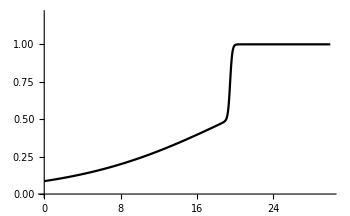

```mathematica
Plot[fAdditionalSigmoidal[0,1,1,8.88,19.5,0.121,0,x],{x,0,30},PlotRange->{0,1.2},ImageSize->350]
```

If we change our function to this form then it behaves exactly in the way we want; but numeric maximum is a big problem!!

15.4758

0.644394

FindArgMax::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

14.8502

16.3688

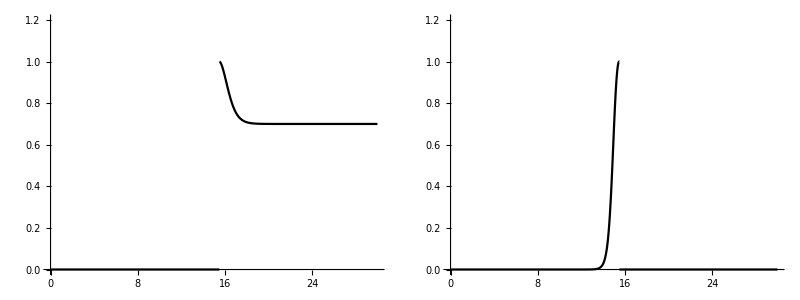
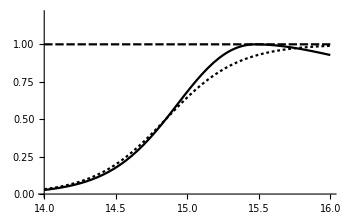
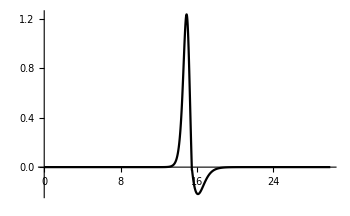

| original | simulation
A11 | 0 | 1.35887×10^-26
A22 | 0.7 | 0.7
Kaa | 1 | 1
B11 | 1 | 1.23579
M11 | 15 | 14.9288
M11_mid | 15 | 14.8502
B22 | -0.15 | -0.217802
LL | 1 | 1.19359
LL_mid | 1 | 1.51857

```mathematica
A11=0; A22=0.7; Kaa=1; B11=4; M11=15; B22=2; LL=1; epsilon=0.02;
(*Plot[1/((1+ⅇ^(-B11*(x-M11)))*(1+ⅇ^(B22*(x-(M11+LL))))),{x,0,30},PlotRange->Full,ImageSize->350]

Plot[Log[1/((1+ⅇ^(-B11*(x-M11)))*(1+ⅇ^(B22*(x-(M11+LL)))))],{x,0,30},PlotRange->Full,ImageSize->350]*)

argument=FindArgMax[Log[(1/((1+ⅇ^(-B11*(x-M11)))*(1+ⅇ^(B22*(x-(M11+LL))))))],{x,M11+LL/2}][[1]]
const=1/((1+ⅇ^(-B11*(argument-M11)))*(1+ⅇ^(B22*(argument-(M11+LL)))))





rightSide[x_]:=UnitStep[x-argument-epsilon]*(1/((1+ⅇ^(-B11*(x-M11)))*(1+ⅇ^(B22*(x-(M11+LL)))))*(Kaa-A22*Kaa)/const+A22*Kaa);
leftSide[x_]:=(1-UnitStep[x-argument-epsilon])*(1/((1+ⅇ^(-B11*(x-M11)))*(1+ⅇ^(B22*(x-(M11+LL)))))*(Kaa-A11*Kaa)/const+A11*Kaa);
wholeFunction[x_]:=rightSide[x]+leftSide[x]






derivativeRightSide[x_]=D[(1/((1+ⅇ^(-B11*(x-M11)))*(1+ⅇ^(B22*(x-(M11+LL)))))*(Kaa-A22*Kaa)/const+A22*Kaa),{x,1}]*UnitStep[x-argument-epsilon];
derivativeLeftSide[x_]=D[(1/((1+ⅇ^(-B11*(x-M11)))*(1+ⅇ^(B22*(x-(M11+LL)))))*(Kaa-A11*Kaa)/const+A11*Kaa),{x,1}]*(1-UnitStep[x-argument-epsilon]);
wholeDerivativeFunction[x_]:=derivativeRightSide[x]+derivativeLeftSide[x]


M11Numeric=FindArgMax[derivativeLeftSide[x],{x,M11}][[1]];
B11Numeric=wholeDerivativeFunction[M11Numeric];
M22Numeric=FindArgMax[Abs[derivativeRightSide[x]],{x,M11+LL}][[1]];
B22Numeric=wholeDerivativeFunction[M22Numeric];
M11mid=x/.FindRoot[wholeFunction[x]==((Kaa-A11)/2+A11),{x,M11}][[1]]
M22mid=x/.FindRoot[wholeFunction[x]==((Kaa-A22)/2+A22),{x,M11+LL}][[1]]
A11Numeric=wholeFunction[0];
A22Numeric=wholeFunction[30];

Grid[{
	{Grid[{
		{Plot[rightSide[x],{x,0,30},PlotRange->{0,1.2},ImageSize->250],
		Plot[leftSide[x],{x,0,30},PlotRange->{0,1.2},ImageSize->250]}
	},Frame->All]},
	{Plot[
		{wholeFunction[x],Kaa,fSigmoidal[A11,Kaa,B11,M11mid,x]}
			,{x,14,16},PlotRange->{0,1.2},ImageSize->350]},
	{Plot[{wholeDerivativeFunction[x]},{x,0,30},PlotRange->Full,ImageSize->350]}
},Frame->All]

m={{,"original","simulation"},
{"A11",A11,A11Numeric},
{"A22",A22,A22Numeric},
{"Kaa",Kaa,Kaa},
{"B11",(1/4)*(Kaa-A11)*B11,B11Numeric},
{"M11",M11,M11Numeric},
{"M11_mid",M11,M11mid},
{"B22",-(1/4)*(Kaa-A22)*B22,B22Numeric},
{"LL",LL,M22Numeric-M11Numeric},
{"LL_mid",LL,M22mid-M11mid}};
Grid[m,Frame->All]
```